-------Monte Carlo Method (Random Sampling)----------

------------------Estimation of Log[2]---------------------

```mathematica
Integrate[1/(1+x),{x,0,1}]
```

Log[2]

```mathematica
Integrate[1/(1+x),{x,0,1}]//N
```

0.693147

```mathematica
Mean[Table[1/(RandomReal[]+1),{10000}]]
```

0.692402

```mathematica
datamon=Table[n=2^k;
{n,Mean[Table[Mean[Table[1/(RandomReal[]+1),{n}]],{1000}]]},{k,5,10}]
```

{{32,0.694258},{64,0.693707},{128,0.693217},{256,0.693039},{512,0.693277},{1024,0.693161}}

```mathematica
datamon//TableForm
```

32 | 0.694258
64 | 0.693707
128 | 0.693217
256 | 0.693039
512 | 0.693277
1024 | 0.693161

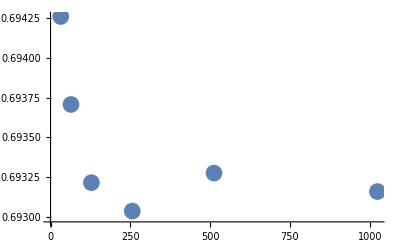

```mathematica
ListPlot[datamon,PlotStyle->PointSize[0.03]]
```

----Estimation of error from actual value--------------------

```mathematica
errdatamon=Table[n=2^k;
{n,Mean[Table[Abs[Mean[Table[1/(RandomReal[]+1),{n}]]-Log[2]],{1000}]]},{k,5,10}]
```

{{32,0.0204507},{64,0.0144277},{128,0.00924035},{256,0.00695217},{512,0.00487888},{1024,0.00343231}}

```mathematica
errdatamon//TableForm
```

32 | 0.0204507
64 | 0.0144277
128 | 0.00924035
256 | 0.00695217
512 | 0.00487888
1024 | 0.00343231

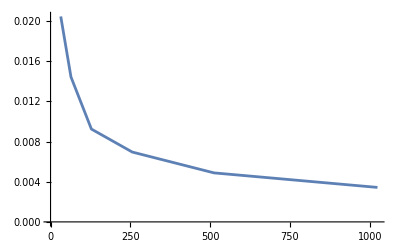

```mathematica
ListPlot[errdatamon,Joined->True]
```

-----How does the error scale with the number of Monte Carlo steps-------

```mathematica
fn[x_]= a3 x^c3
```

a3 x^c3

```mathematica
fit=FindFit[errdatamon,{a3 x^c3},{a3,c3},{x}]
```

{a3→0.12745,c3→-0.528043}

```mathematica
fn[x]/.fit
```

0.12745/x^0.528043

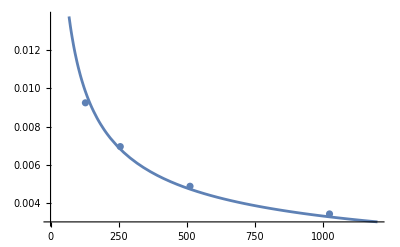

```mathematica
Show[Plot[fn[x]/.fit,{x,0,1200}],ListPlot[errdatamon]]
```

------------------Estimation of Pi---------------------

```mathematica
Integrate[4/(1+x^2),{x,0,1}]
```

π

```mathematica
datamonpi=Table[n=2^k;
{n,Mean[Table[Mean[Table[4/(RandomReal[]^2+1),{n}]],{1000}]]},{k,5,10}]
```

{{32,3.1413},{64,3.14241},{128,3.14472},{256,3.14068},{512,3.14265},{1024,3.14136}}

```mathematica
datamonpi//TableForm
```

32 | 3.1413
64 | 3.14241
128 | 3.14472
256 | 3.14068
512 | 3.14265
1024 | 3.14136

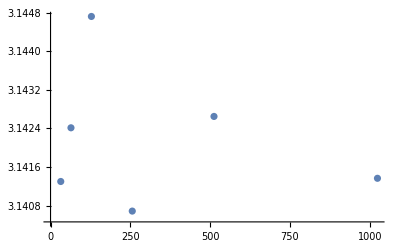

```mathematica
ListPlot[datamonpi]
```

```mathematica
errdatamonpi=Table[n=2^k;
{n,Mean[Table[Abs[Mean[Table[4/(RandomReal[]^2+1),{n}]]- π],{1000}]]},{k,5,10}]
```

{{32,0.0919924},{64,0.0650959},{128,0.0442099},{256,0.0333097},{512,0.0233857},{1024,0.0162281}}

```mathematica
errdatamonpi//TableForm
```

32 | 0.0919924
64 | 0.0650959
128 | 0.0442099
256 | 0.0333097
512 | 0.0233857
1024 | 0.0162281

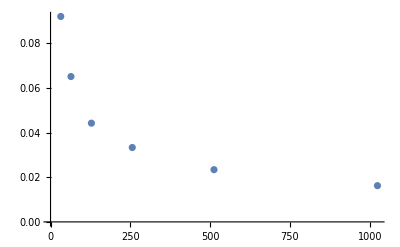

```mathematica
ListPlot[errdatamonpi]
```

------------------------------Importance Sampling--------------------

------------------Estimation of Pi using Importance Sampling-------------------- -

```mathematica
Integrate[Exp[-x],{x,0,1}]
```

(-1+ⅇ)/ⅇ

```mathematica
p[x_]:=Exp[1-x]/(Exp[1.0]-1)
```

```mathematica
Dist=ProbabilityDistribution[p[x],{x,0,1}];
```

```mathematica
PDF[Dist,x]
```

Piecewise[{{0.581977 ⅇ^(1-x), 0<x<1}, {0, True}}]

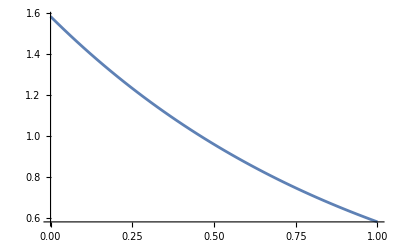

```mathematica
Plot[PDF[Dist,x],{x,0,1}]
```

```mathematica
RandomVariate[Dist,100];
```

```mathematica
Mean[Dist]
```

0.418023

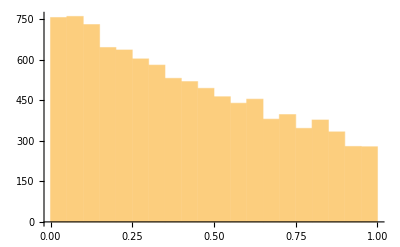

```mathematica
Histogram[RandomVariate[Dist,10000]]
```

```mathematica
f[x_]:=4/(1+x^2)
```

```mathematica
dataimppi=Table[n=2^k;
{n,Mean[Table[Mean[Table[xi=RandomVariate[Dist,2][[1]];f[xi]/p[xi],{n}]],{2}]]},{k,5,10}]
```

{{32,3.16564},{64,3.13155},{128,3.16453},{256,3.17263},{512,3.13761},{1024,3.15086}}

```mathematica
dataimppi//TableForm
```

32 | 3.16564
64 | 3.13155
128 | 3.16453
256 | 3.17263
512 | 3.13761
1024 | 3.15086

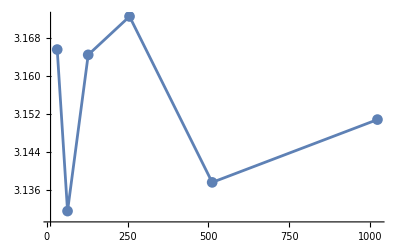

```mathematica
ListPlot[dataimppi,Joined->True,PlotRange->Full,PlotMarkers->Automatic]
```

------------------------Using a different probability distribution for importance sampling for Pi estimation--------------

```mathematica
Integrate[Exp[-x^2],{x,0,1}]
```

-1/2 √π (-1+Erfc[1])

```mathematica
p1[x_]:=Exp[-x^2]/(-1/2 √π (-1+Erfc[1]))
```

```mathematica
Dist1=ProbabilityDistribution[p1[x],{x,0,1}];
```

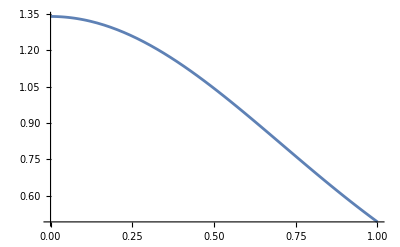

```mathematica
Show[Plot[PDF[Dist1,x],{x,0,1}]]
```

```mathematica
f1[x_]:=4/(1+x^2)
```

```mathematica
dataimppi1=Table[n=2^k;
{n,Mean[Table[Mean[Table[xi=RandomVariate[Dist1,2][[1]];f1[xi]/p1[xi],{n}]],{2}]]},{k,5,10}]
```

{{32,3.14056},{64,3.13729},{128,3.15245},{256,3.14497},{512,3.13684},{1024,3.15113}}

```mathematica
dataimppi1//TableForm
```

32 | 3.14056
64 | 3.13729
128 | 3.15245
256 | 3.14497
512 | 3.13684
1024 | 3.15113

-------Comparison of two different probability distribution for Importance Sampling--------

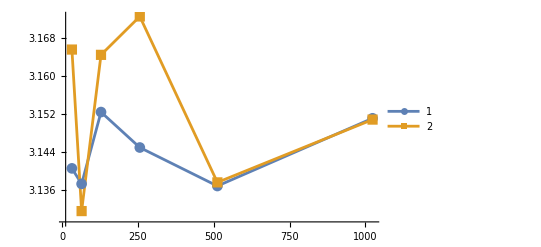

```mathematica
ListPlot[{dataimppi1,dataimppi},Joined->True,PlotRange->Full,PlotMarkers->Automatic,PlotLegends->Automatic]
```

--------------------Needle Drop experiment on a circle of radius 1, enclosed within a square of side 2----------

```mathematica
RandomReal[{0,1},2]
```

{0.687483,0.829117}

```mathematica
RandomReal[{0,1},2]^2
```

{0.231984,0.376517}

```mathematica
RandomReal[{0,1},2]^2//Total
```

1.40579

```mathematica
If[(RandomReal[{0,1},2]^2//Total)<=1,1,0]
```

1

```mathematica
Table[If[(RandomReal[{0,1},2]^2//Total)<=1,1,0],{100}]
```

{0,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,1,0,0,1,1,1,1,1,1,1,1,1,1,0,0,0,0,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,0,1,1,1,0,1,1,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,0,1,1,1,1,0,1,1,1,0,1,1,1,0,1,0}

```mathematica
Table[If[(RandomReal[{0,1},2]^2//Total)<=1,1,0],{100}]//Total
```

78

```mathematica
1/100(Table[If[(RandomReal[{0,1},2]^2//Total)<=1,1,0],{100}]//Total)4.0
```

3.12

```mathematica
dataset= Table[nMax=10000;1/nMax(Table[If[(RandomReal[{0,1},2]^2//Total)<=1,1,0],{nMax}]//Total)4.0,{1000}];
```

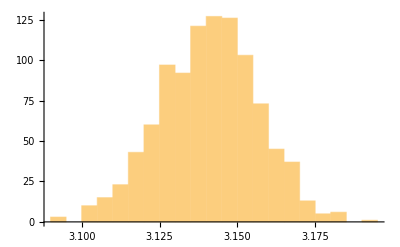

```mathematica
Histogram[dataset]
```

```mathematica
Mean[dataset]
```

3.14104

---------Histogram of uniform distribution-------

```mathematica
data1=Table[RandomReal[],10000]; (*between 0 and 1*)
```

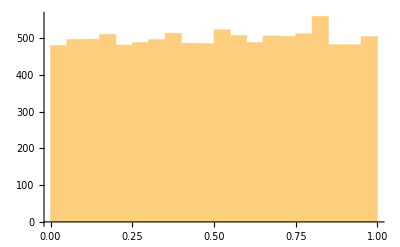

```mathematica
Histogram[data1]
```

```mathematica
data11=Table[RandomReal[{0,4}],10000]; (*between 0 and 4*)
```

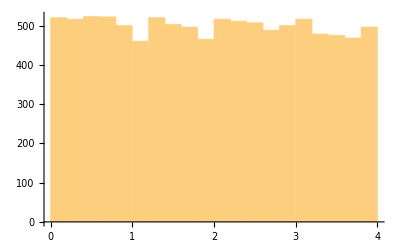

```mathematica
Histogram[data11]
```

-------We have seen that if the Jacobian A =  (a | b
c | d) where a,b,c,d are drawn from a uniform distribution, roughly half of them will give saddle point. Draw the numbers a,b,c,d from a Normal Distribution with mean zero and standard deviation unity. What fraction of numbers will yield saddle?---------

```mathematica
alist= Table[RandomVariate[NormalDistribution[]],{i,1,1000}]; (*checking the nomral distribution*)
```

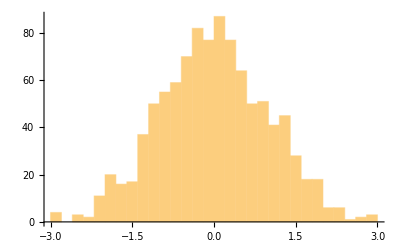

```mathematica
Histogram[alist]
```

```mathematica
sadlist=Table[alist= Table[RandomVariate[NormalDistribution[]],{i,1,Nmat}]; (*data list for a*)
blist= Table[RandomVariate[NormalDistribution[]],{i,1,Nmat}];(*data list for b*)
clist= Table[RandomVariate[NormalDistribution[]],{i,1,Nmat}];(*data list for c*)
dlist= Table[RandomVariate[NormalDistribution[]],{i,1,Nmat}];(*data list for d*)
deltalist = alist dlist - blist clist;
fracsaddle = Total[1-UnitStep[deltalist]]/Length[deltalist]//N; (*if deltalist<0 it is a saddle*){Nmat,fracsaddle},{Nmat, 1,100,1}];
```

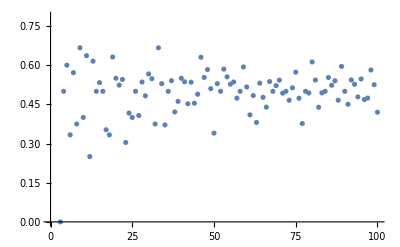

```mathematica
ListPlot[sadlist]
```

------Examples of Integration With limits other than 0 to 1 --------

```mathematica
Integrate[1/(√(2π))Exp[-x^2/2],{x,-3,3}]//N
```

0.9973

```mathematica
datamonpi1=Table[n=2^k;
{n,6Mean[Table[Mean[Table[1/(√(2π))Exp[-RandomReal[{-3,3}]^2/2],{n}]],{1000}]]},{k,5,15}];
```

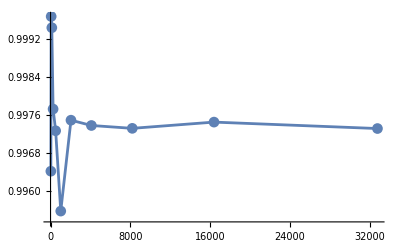

```mathematica
ListPlot[datamonpi1,Joined->True,PlotMarkers->Automatic]
```

----- Example 2 With limits other than 0 to 1 --------

```mathematica
Integrate[√(x+√(x+√(x+√x))),{x,0,4}]//N
```

7.67661

```mathematica
datamonpi2=Table[n=2^k;
{n,4 Mean[Table[Mean[Table[√(RandomReal[{0,4}]+√(RandomReal[{0,4}]+√(RandomReal[{0,4}]+√RandomReal[{0,4}]))),{n}]],{100}]]},{k,10,15}]
```

{{1024,7.81041},{2048,7.81661},{4096,7.82094},{8192,7.82279},{16384,7.82057},{32768,7.81987}}

--------------Try Importance Sampling for the same exercise----------

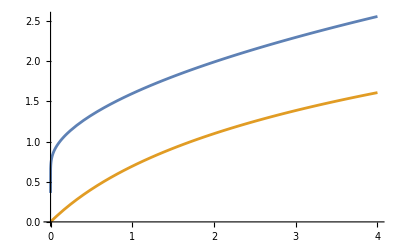

```mathematica
Plot[{√(x+√(x+√(x+√x))),Log[x+1]},{x,0,4}]
```

```mathematica
Integrate[Log[x+1],{x,0,4}]//N
```

4.04719

```mathematica
p2[x_]:=Log[x+1]/4.047189562170502
```

```mathematica
Dist2=ProbabilityDistribution[p2[x],{x,0,4}];
```

```mathematica
PDF[Dist2,x]
```

Piecewise[{{0.247085 Log[1+x], 0<x<4}, {0, True}}]

```mathematica
test = RandomVariate[Dist2,10000];
```

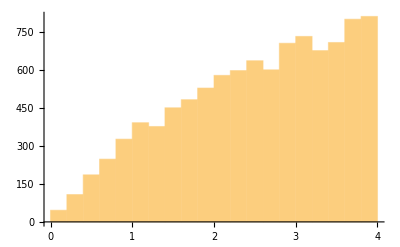

```mathematica
Histogram[test]
```

```mathematica
f2[x_]:=√(x+√(x+√(x+√x)))
```

```mathematica
dataimppi2=Table[n=2^k;
{n, Mean[Table[Mean[Table[xi=RandomVariate[Dist2,2][[1]];f2[xi]/p2[xi],{n}]],{1}]]},{k,5,10}]
```

{{32,7.8681},{64,7.17708},{128,7.66552},{256,7.89221},{512,7.48608},{1024,7.71621}}

--------Example 3 Random Sampling with limits other than 0 and 1-------

```mathematica
Integrate[4/(1+x^2),{x,1,3}]//N
```

1.85459

```mathematica
datamonpi=Table[n=2^k;
{n,2  Mean[Table[Mean[Table[4/(RandomReal[{1,3}]^2+1),{n}]],{1000}]]},{k,5,10}]
```

{{32,1.86025},{64,1.8523},{128,1.8535},{256,1.85698},{512,1.85665},{1024,1.85543}}

------Example 3 Importance Sampling ---

```mathematica
Integrate[Exp[-x],{x,1,3}]//N
```

0.318092

```mathematica
p3[x_]:=Exp[-x]/0.3180923728035784
```

```mathematica
Dist3=ProbabilityDistribution[p3[x],{x,1,3}];
```

```mathematica
test1 =RandomVariate[Dist3,10000];
```

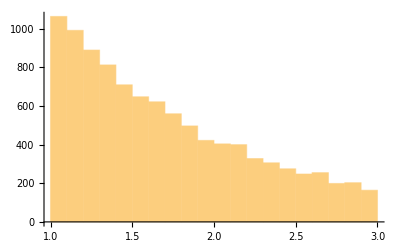

```mathematica
Histogram[test1]
```

```mathematica
f3[x_]:=4/(1+x^2)
```

```mathematica
dataimppi1=Table[n=2^k;
{n,Mean[Table[Mean[Table[xi=RandomVariate[Dist3,2][[1]];f3[xi]/p3[xi],{n}]],{2}]]},{k,1,2}]
```

{{2,1.73903},{4,1.77781}}